```mathematica
`
```

# Polymer Dispersity

## Random Polymers: A Polymer as a Random Walk

### The simplest model of polymer morphology is a sequence of uncorrelated bond lengths. This can be modeled with a random walk.

#### Uncorrelated Random Walk Model of a Polymer

We will fix the bond length to be equal to 2 and visualize the polymers as spheres of radius 1.

Here are two quick examples of visualizing such a random walk with 32 molecular units

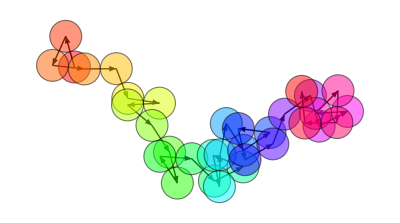

```mathematica
steps = AngleVector[{2,#}]&/@RandomReal[{0,2π},32];
positions = Prepend[Accumulate[steps],{0,0}];
Graphics[

]
```

In 3 dimensions, we can use points on a sphere of radius 2 for the step directions

```mathematica
steps = RandomPoint[Sphere[{0,0,0},2],32];
positions = Prepend[Accumulate[steps],{0,0,0}];
Graphics3D[

]
```

-Graphics3D-

#### Expected Length of an Uncorrelated Polymer as a Function of the Number of Units

We can use a Monte Carlo method to generate a set of random walks for a fixed number of units, an then compute the mean of the displacement from the origin of the walk.  Then we can repeat this for different numbers of units.

This function returns the net displacement of an uncorrelated random walk with step lengths of 1

```mathematica
Norm[
Total[ (*net displacement vector*)
RandomPoint[Sphere[],10] (*unit length steps*)
]
]
```

3.25297

```mathematica
displacement[nUnits_, dimension_/;1<= dimension<= 3]:=
 Norm[
Total[ (*net displacement vector*)
Which[
dimension==1,RandomChoice[{-1,1}],
dimension==2,RandomPoint[Circle[],nUnits],
True,RandomPoint[Sphere[],nUnits]
]
]
]
```

Making sample sizes of 1000 for different numbers of units and computing their means and standard deviations.

```mathematica
displacementData = Table[{2^units,displacement[2^units, 3]},{units,1,18},1000];
(*computation takes about 30 seconds*)
```

```mathematica
meanDisplacements = Mean/@displacementData;
standardDeviationDisplacements = StandardDeviation/@displacementData;
```

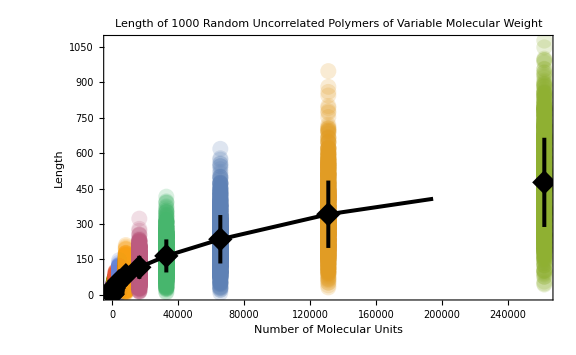

```mathematica
Show[
ListPlot[displacementData,],ListLinePlot[MapThread[{#1,Around[#2,#3]}&,{First/@meanDisplacements,Last/@meanDisplacements,Last/@standardDeviationDisplacements}],]
]
```

Let’s see if we can discover the relation between the expected length and number of units

```mathematica
model = a (n)^power;
fit = FindFit[meanDisplacements,model,{a,power},n]
```

{a→0.868782,power→0.505816}

```mathematica
fitModel = model/.fit
```

0.868782 n^0.505816

The fit shows that the length increases as 
In our simulation, each If each bond had length = 1.  If the bond length were a, then the results would have been

George, if I had a way to insert “extra stuff, or footnote stuff, I would relate this to diffusion.

```mathematica
probabilityOfAtomPosition3D =Exp[-x^2/(4 diffCoeff t)]/((4 Pi  diffCoeff t )^(3/2))
```

(ⅇ^(-x^2/(4 diffCoeff t)))/(8 π^(3/2) (diffCoeff t)^(3/2))

normalized

```mathematica
Integrate[4 Pi x^2  probabilityOfAtomPosition3D,{x,0,Infinity}, Assumptions->diffCoeff> 0 && t> 0]
```

1

Mean displacement

```mathematica
Integrate[4 Pi x^3  probabilityOfAtomPosition3D,{x,-Infinity,Infinity}, Assumptions->diffCoeff> 0 && t> 0]
```

0

Mean squared displacement

```mathematica
msqd =Integrate[4 Pi x^4  probabilityOfAtomPosition3D,{x,-Infinity,Infinity}, Assumptions->diffCoeff> 0 && t> 0]
```

12 diffCoeff t

```mathematica
Sqrt[msqd/.diffCoeff->1/6]
```

√2 √t

????
 The coefficient seems closer to 1 than .  Does the diffusion equation approximation must over estimate the RMS displacement.  This is reasonable as the derivation produces particles that travel infinitely fast, so there is something in Stirling’s appx that maybe is accounting for this error
 ???

End Footnote

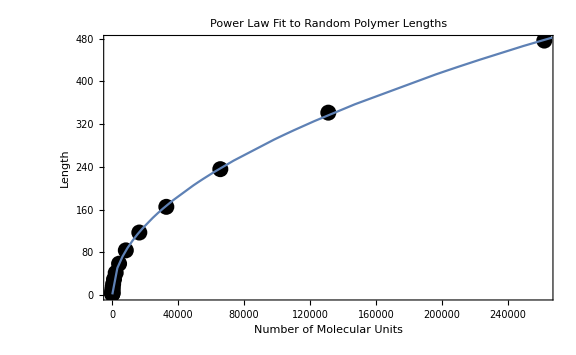

```mathematica
Show[
ListPlot[meanDisplacements,
],
Plot[fitModel,{n,1,10^7}]]
```

Thus, we demonstrate that the expected length polymer with uncorrelated bond direction increases as the square-root of the number of molecular units.

## “Models of Stiff Polymers” Creating a Polymer with Correlations

Some polymers may be less “floppy”: there will be a smaller range of “bending angle” at each molecular unit.
This would create direction correlations in the polymer chain. 

We can model this by creating a correlation in the steps by selecting new directions within a given angle of the previous angle.

In two dimensions, this would be an arc of a circle centered on the previous direction.  In three dimensions, this would be points withing a given solid angle on a sphere.

Two dimensions is  straightforward.  The next direction is chosen from a uniform distribution of angles around the last direction  Δϕ < θ < Δϕ.   AnglePath does exactly this:

```mathematica
Manipulate[
With[{steps = AnglePath[{2,#}&/@RandomReal[{-range/2,range/2},12]]},
Graphics[

]
],
{range,0,2Pi}
]
```

For three dimensions, we need an algorithm to produce random points from a uniform spatial distribution over a spherical cap.
Such an algorithm is not difficult, but would be a distraction from our immediate purposes.
A brute force method would be to generate very many random points on a sphere, and then select only those that lie within a given angle of  a given direction.
For example, is a set of random points within a solid angle of 5° of {1,0,0}

```mathematica
Graphics3D[Point@With[{rp = RandomPoint[Sphere[],10^6]}, Select[#.{1,0,0}> Cos[5Degree]&][rp]]
]
```

-Graphics3D-

And then we can rotate those points to any direction:

```mathematica
rotatedSet =Module[{direction={1,2,3},initialPoints=RandomPoint[Sphere[],10^6],randomPoints,rotationOperator},randomPoints=Select[#1.{1,0,0}>Cos[5 °]&][initialPoints];rotationOperator=RotationTransform[{{1,0,0},direction}];rotationOperator[randomPoints]];
Graphics3D[]
```

-Graphics3D-

For our calculations, we can use memoization to precompute random points.  To keep the number of random points in our sets about the same, we need to scale the amount of initial points on the sphere by dividing by the surface area of a spherical cap--that surface area goes like 1-cos(ϕ)

```mathematica
Clear[randomPoints]
```

```mathematica
randomPoints[solidAngle_]:= (randomPoints[solidAngle]=With[{rp = RandomPoint[Sphere[],Round[10^4/(1-Cos[solidAngle])]]}, Select[#.{1,0,0}> Cos[solidAngle]&][rp]])
```

To create this correlated walk, we take the last two points on a random walk’s path and use that to determine the direction.  We can use that direction to rotate a point chosen from the spherical cap (that we have centered on {1,0,0}, and then append that selection to the path.

```mathematica
addToPath[path_,solidAngle_, r_]:= 
Module[{lastDirection = path[[-1]]-path[[-2]],rotationMatrix},
rotationMatrix=RotationMatrix[{{1,0,0 },lastDirection}];Append[path,path[[-1]] + r rotationMatrix.RandomChoice[randomPoints[solidAngle]]
]
]
```

We can always select the first point and first direction of the random walk:

```mathematica
initialPath = {{0,0,0},{2,0,0}}
```

{{0,0,0},{2,0,0}}

For example, the following simulates polymers with 40 units that don’t bend more than 5^◦, 30^◦,60^◦, 90^◦ at each turn

```mathematica
With[
{graphics =Table[
path=Nest[addToPath[#1,deg °,2]&,initialPath,40];,
{deg,{5,30,60,90}}]},
Grid[Partition[graphics,2]]
]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

#### Simulating expected length of a “stiff” polymer

As before we can construct data for differing numbers of units. 

(This isn’t very efficient code because we are repeatedly appending new points to a path.  It could be made more efficient by keeping only the last point and the last direction and using Fold[...].  However, this will be fine if we are patient.)

```mathematica
displacement[units_, floppiness_, r_]:= 
Last[Nest[addToPath[#,floppiness ,1]&,{{0,0,0},{0,0,1}},units]]
```

```mathematica
data =Table[{2^units,Norm[displacement[2^units, 10 Degree,1]]},{units,1,10},250];
(*takes about a minute*)
```

```mathematica
meanDisplacements = Mean/@data;
standardDeviationDisplacements = StandardDeviation/@data;
```

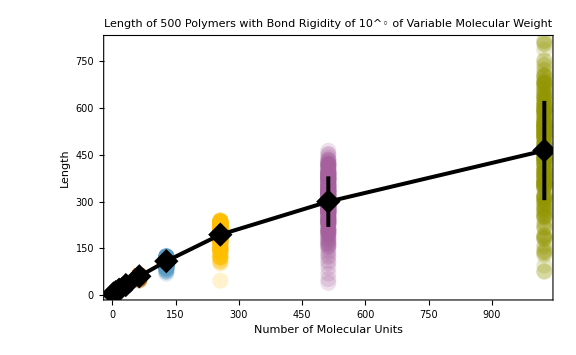

```mathematica
Show[
ListPlot[data,],ListLinePlot[MapThread[{#1,Around[#2,#3]}&,{First/@meanDisplacements,Last/@meanDisplacements,Last/@standardDeviationDisplacements}],]
]
```

Finding the power law fit:

```mathematica
fit=FindFit[Flatten[data,1],model,{a,power},n];
model/.fit
```

3.7264 n^0.698339

Finding the power law as a function of the polymer rigidity

```mathematica
rigidityFit[rigidity_,simulations_?IntegerQ]:=
 Block[{
data=Table[{2^units,Norm[displacement[2^units,rigidity °,1]]},{units,1,10},simulations],
a,n,power
},
Flatten[{rigidity,{a,power}/.FindFit[Flatten[data,1],a n^power,{a,power},n]}]
]
```

```mathematica
results =rigidityFit[#,500]&/@{5,10,15,30,45,90,180};
```

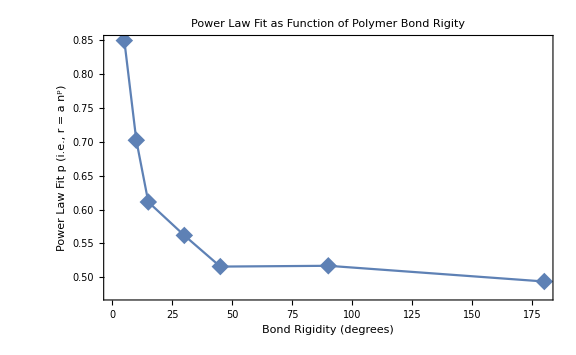

```mathematica
ListLinePlot[results[[All,{1,3}]], ]
```

#### The power law dependence on rigidity can be computed by the correlation method described in Section 7.2 of Kinetics of Materials by Baluffi, Allen, Carter